```mathematica
eqn = J*ω'[t] == Tm-kq*ρ*d^5*ω[t]^2;
params = {J->5.7258*^-4, kq->2.4968*^-5, ρ->1.205, d->0.1270};
```

```mathematica
ωSol = ω/.First@DSolve[eqn,ω,t]
```

Function[{t},(√Tm Tanh[(d^(5/2) √kq t √Tm √ρ+d^(5/2) J √kq √Tm √ρ C[1])/J])/(d^(5/2) √kq √ρ)]

```mathematica
ωSol[t]//TrigToExp//Simplify
```

((-1+ⅇ^((2 d^(5/2) √kq √Tm √ρ (t+J C[1]))/J)) √Tm)/(d^(5/2) (1+ⅇ^((2 d^(5/2) √kq √Tm √ρ (t+J C[1]))/J)) √kq √ρ)

```mathematica
$ωSol[Tm_,t_]=ωSol[t]/.Join[params,{C[1]->0}]
```

31718. √Tm Tanh[1746.48 (0.+0.0000315279 t √Tm)]

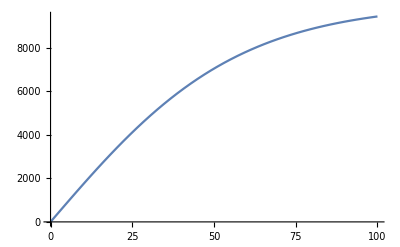

```mathematica
Plot[$ωSol[0.1,t],{t,0,100}, PlotRange->Full]
```